```mathematica
SetDirectory["/Users/joshsilverman/Documents/Research/AutoFilter/gogat_isocsv"]
scored=Import["gogat40_iso_scored.csv","Data"];
```

/Users/joshsilverman/Documents/Research/AutoFilter/gogat_isocsv

```mathematica
Position[scored[[1]],"SCORE"]
```

{{154}}

```mathematica
(*ampu = 13*)
(*ampl = 14*)
(*score = 154*)
(*protein ID = 141*)
```

```mathematica
proteins=DeleteDuplicates[Transpose[scored[[2;;-1]]][[141]]];
```

```mathematica
proteins
```

{P25665,P0A6F3,Q8FBC3,P08200,P04949,P36683,P0A6M8,P0A6N1,P21420,P0ABH7}

```mathematica
ratios={};
Do[
line=scored[[j]];
ampu = line[[13]];
ampl = line[[14]];
protein = line[[141]];
score = line[[154]];
AppendTo[ratios,{{First[Flatten[Position[proteins, protein]]],ampl/(ampu+ampl)},score}];
,{j,2,Length[scored]}
];
```

```mathematica
cutoff = 100;
filteredratios={};
Do[
score = ratios[[i]][[2]];
points = ratios[[i]][[1]];
If[score < cutoff,AppendTo[filteredratios, points+{0,0}]];
,{i,1,Length[ratios]}
];
```

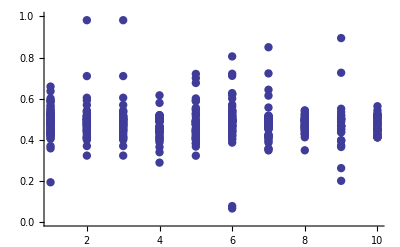

```mathematica
p100=ListPlot[filteredratios,PlotRange->{All,{0,1}},PlotStyle->Directive[PointSize[0.015]]]
```

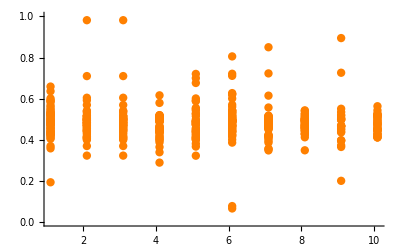

```mathematica
p10=ListPlot[filteredratios,PlotRange->{All,{0,1}},PlotStyle->Directive[PointSize[0.015],Orange]]
```

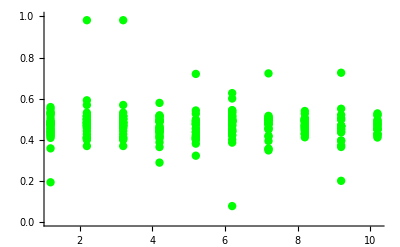

```mathematica
p1=ListPlot[filteredratios,PlotRange->{All,{0,1}},PlotStyle->Directive[PointSize[0.015],Green]]
```

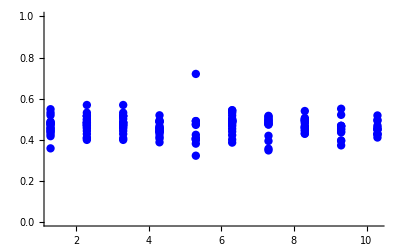

```mathematica
p12=ListPlot[filteredratios,PlotRange->{All,{0,1}},PlotStyle->Directive[PointSize[0.015],Blue]]
```

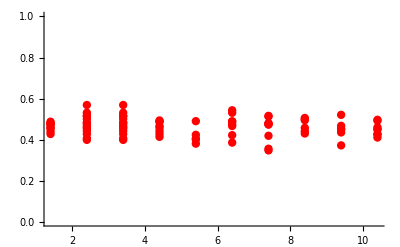

```mathematica
p13=ListPlot[filteredratios,PlotRange->{All,{0,1}},PlotStyle->Directive[PointSize[0.015],Red]]
```

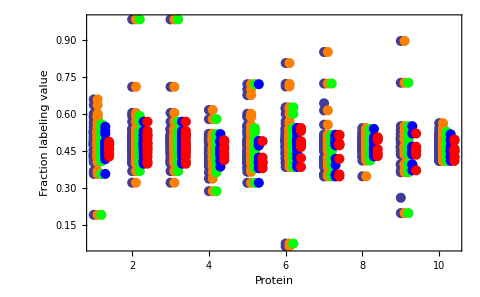

```mathematica
Show[p100,p10,p1,p12,p13,AxesOrigin->{0,0},LabelStyle->Directive[FontSize->22,FontFamily->"Helvetica"],Frame->True,PlotRange->All,FrameLabel->{"Protein","Fraction labeling value"}]
```